# On Distributions. How A Fnc Identity Opens Up To Different Distribution Families.

[see -> BSSRDF -> Correlated Media -> Casasanta & Garra 2018 vs Jarabo/Wrenninge Gamma-mixture]

Two transmittance laws, from two different fields, turn out to be exactly the same formula at a specific point (α=1). Despite this, the underlying constructions are completely different: one starts from a fixed event rate and a reweighted event count, while the other introduces a Gamma-distributed random rate.

This notebook investigates the probability model connecting the two. We derive the role of α, examine the α→∞ limit and its relation to classical transport, and eventually identify the resulting distribution as the Lomax distribution. Along the way, we compare the probabilistic construction with the formulations given in the relevant literature. 

All just as an excuse to dive into distribution mechanics for light transport theory.

Two Source Formulas

[see -> Casasanta & Garra 2018 - Towards a Generalized Beer-Lambert Law, Eq. 6, Section 4]
Their inhomogeneous weighted-Poisson construction, at the Mittag-Leffler weight's ν=1 special case, collapses to a plain hyperbolic law. As stated in their own Eq. 6, using x0 for their constant:

T(x)=1/(x+x0)

Note this does not satisfy T(0)=1, which any genuine survival function must (a photon must survive zero distance with certainty). Their own stated equation is not properly normalized for use as a Monte Carlo free-flight distribution. The corrected form, with x0 now playing the role of a genuine scale parameter, is:

T_hyp(x)=x0/(x+x0)

x0 is the only free parameter here, and it is not an arbitrary curve-fitting constant -- it is the scale at which the medium’s (deterministic, in this construction) density profile λ(x)=ln(x+x0) actually varies. This formula comes from a weighted-Poisson mechanism: the extinction rate itself stays fixed and deterministic at every point -- what gets reweighted is the probability of the event count, not the rate. There is no randomization of σ anywhere in this derivation, which is exactly why it sits outside the Jensen’s-inequality bound that constrains the next formula below.

[see -> 
Jarabo, Aliaga & Gutierrez 2018 (5.2 - An intuitive local model for positively-correlated media); 
Wrenninge, Villemin & Hery 2017, Pixar Technical Memo 17-07]

The Gamma-mixture transmittance, general α:

T_GL(t)=(1+(σ t)/β)^-α

Here, by contrast, σ itself is a randomized extinction rate, drawn from a Gamma distribution with shape α and scale β -- the transmittance above is the ensemble average ⟨Exp[-σ t]⟩ over that distribution, not a curve chosen to resemble one. α controls how variable the rate is across realizations (smaller α means a heavier, more clustered medium); β sets its scale. Because Exp[-σ t] is convex in σ, Jensen’s inequality applies unconditionally here: this transmittance can only ever sit at or above classical, for any choice of α and β whatsoever.

α=1 is not an arbitrary point to check -- it is the specific case where the Gamma distribution over σ collapses to a plain exponential distribution (Gamma with shape 1 is exponential, exactly, not approximately). That is the real reason the identity below lands where it does: 
- one formula comes from a fixed rate with a reweighted event count, 
- the other from an exponentially-distributed randomized rate 
two genuinely different mechanisms, meeting at the one point where the second one’s own randomness takes its simplest possible form.

[see -> earlier derivation, following Davis & Xu (DX14), cited by Wrenninge et al. 2017]
α has a precise statistical meaning, not just a qualitative one. If σ is Gamma-distributed with mean σbar and shape α, its coefficient of variation is fixed entirely by α:

```mathematica
gammaRate = GammaDistribution[alpha, sigmabar/alpha]
```

GammaDistribution[alpha,sigmabar/alpha]

```mathematica
meanCheck = Mean[gammaRate] // FullSimplify
```

sigmabar

```mathematica
(* Expect: sigmabar, confirming this parameterization keeps the mean rate exactly sigmabar regardless of alpha *)
```

```mathematica
cvSquared = Variance[gammaRate]/Mean[gammaRate]^2 // FullSimplify
```

1/alpha

```mathematica
(* Expect: 1/alpha, i.e. CV^2 = 1/alpha exactly *)
```

```mathematica
FullSimplify[1/cvSquared - alpha]
```

0

```mathematica
(* Expect: 0, confirming alpha = 1/CV^2 exactly, not just approximately or asymptotically *)
```

So α=1 is not merely ‘a special value that happens to work’ -- it is the specific point where CV^2=1, the exact coefficient of variation of a plain exponential distribution. Every distribution in this family with α≠1 has σ more tightly or more loosely concentrated around its mean than exponential; α=1 is the unique crossing point where that concentration matches the classical case exactly, which is the deeper reason the identity below lands there rather than anywhere else.

Seeing this directly: the shape of the σ-distribution itself, at several α, all holding the same mean σbar fixed.

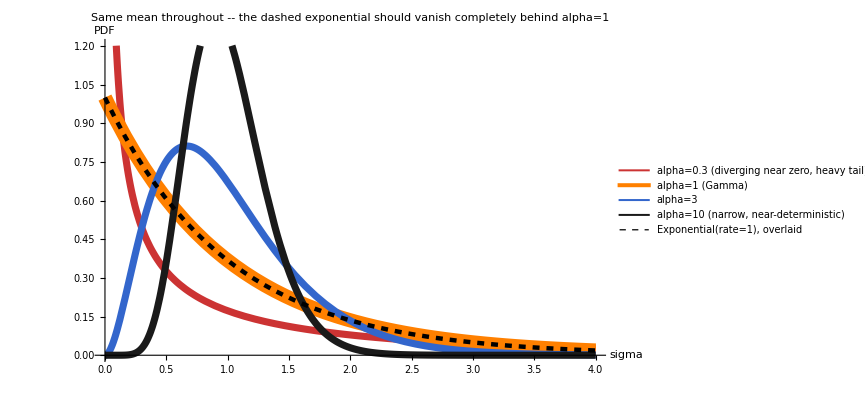

```mathematica
Plot[Evaluate[Join[
	Table[
	PDF[GammaDistribution[a, 1/a], sig], {a, {0.3, 1, 3, 10}}], {
	PDF[ExponentialDistribution[1], sig]}]], {sig, 0, 4}, 
	PlotStyle -> {{RGBColor[0.8, 0.2, 0.2], Thickness[0.008]}, 
	{RGBColor[1, 0.5, 0], Thickness[0.016]}, {RGBColor[0.2, 0.4, 0.8], Thickness[0.008]}, 
	{RGBColor[0.1, 0.1, 0.1], Thickness[0.008]}, {Black, Dashed, Thickness[0.005]}}, 
	PlotLegends -> {"alpha=0.3 (diverging near zero, heavy tail)", "alpha=1 (Gamma)", 
	"alpha=3", "alpha=10 (narrow, near-deterministic)", 
	"Exponential(rate=1), overlaid"}, AxesLabel -> {"sigma", "PDF"}, 
	PlotLabel -> "Same mean throughout -- the dashed exponential should vanish completely behind alpha=1", 
	ImageSize -> 640]
```

The dashed black curve is an independently-defined exponential, plotted on top of, not derived from, the alpha=1 Gamma curve.
At the other end, alpha=0.3 is not a wide, spread-out bump : it diverges toward infinity right at σ=0 (the Gamma density behaves like σ^(α-1) near the origin, which blows up whenever α<1) and then decreases monotonically -- more concentrated at zero than the exponential itself, not less, with a correspondingly heavier tail out at large σ to keep the total probability equal to one. Large α collapses the distribution toward a narrow spike at the mean instead -- exactly the α→∞ limit where the randomized rate stops being random at all and the whole family reduces back to plain classical transport.

And the crossing point itself, directly: CV as a function of alpha.

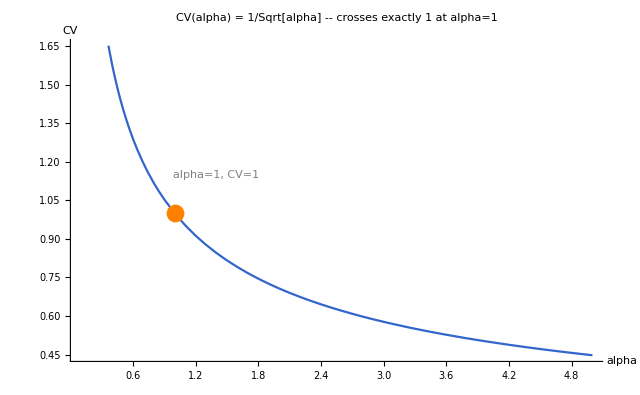

```mathematica
Plot[1/Sqrt[a], {a, 0.1, 5}, 
	Epilog -> {RGBColor[1, 0.5, 0], PointSize[0.02], Point[{1, 1}], GrayLevel[0.5], Text["alpha=1, CV=1", {1.4, 1.15}]}, 
	AxesLabel -> {"alpha", "CV"}, 	PlotLabel -> "CV(alpha) = 1/Sqrt[alpha] -- crosses exactly 1 at alpha=1", 
	PlotStyle -> RGBColor[0.2, 0.4, 0.8], ImageSize -> 640]
```

At the specific value α=1, this is what we compare against the hyperbolic law above.

Symbolic Identity Check

Define both transmittance functions exactly as stated above.

```mathematica
Clear[x, x0, t, sigma, beta, alpha, Thyp, TGL]
```

```mathematica
Thyp[x_, x0_] := x0/(x + x0)
```

```mathematica
TGL[t_, sigma_, alpha_, beta_] := (1 + sigma*t/beta)^(-alpha)
```

The claim: TGL at α=1, with β=σ×x0, is identical to Thyp. Substitute and simplify:

```mathematica
TGLAlpha1 = TGL[t, sigma, 1, sigma*x0] // Simplify
```

x0/(t+x0)

```mathematica
(* Expect: x0/(t+x0), matching Thyp[t, x0] exactly *)
```

```mathematica
identityCheck = Simplify[Thyp[t, x0] - TGLAlpha1]
```

0

```mathematica
(* Expect: 0, confirming the two are algebraically identical, not just numerically close *)
```

Take care that this is a symbolic check, not a numerical spot-check -- Simplify returning exactly 0 (not merely a small residual) is the actual proof of identity.

Confirming the Densities Match Too

A survival-function identity should imply the corresponding densities are identical too, since p(t) = -dT/dt. Build both as genuine ProbabilityDistribution objects, and compare the derived densities directly.

```mathematica
distHyp = ProbabilityDistribution[{"CDF", 1 - Thyp[x, x0]}, {x, 0, Infinity}]
```

ProbabilityDistribution[Piecewise[{{x0/(x+x0)^2, x>0}, {0, True}}],{x,0,∞}]

```mathematica
distGL = ProbabilityDistribution[{"CDF", 1 - TGL[t, sigma, 1, sigma*x0]}, {t, 0, Infinity}]
```

ProbabilityDistribution[Piecewise[{{1/((1+x/x0)^2 x0), x>0}, {0, True}}],{x,0,∞}]

```mathematica
pdfHyp = PDF[distHyp, x]
```

Piecewise[{{x0/(x+x0)^2, x>0}, {0, True}}]

```mathematica
pdfGL = PDF[distGL, t] /. t -> x
```

Piecewise[{{1/((1+x/x0)^2 x0), x>0}, {0, True}}]

```mathematica
Simplify[pdfHyp - pdfGL]
```

0

```mathematica
(* Expect: 0 again, confirming both the survival function AND the density coincide exactly *)
```

Numerical Cross-Check

A concrete numeric instance, matching the specific values.

```mathematica
N[Thyp[3.0, 2.0]]
```

0.4

```mathematica
N[TGL[3.0, 1.0, 1, 2.0]]
```

0.4

```mathematica
(* Both should give exactly 0.4 -- x0/(x+x0) = 2/(3+2) = 0.4 *)
```

Visualizing the Identity

Three plots, in order of increasing strictness. 
- First, the two curves overlaid directly -- if they truly coincide, the second (dashed) curve should be hidden exactly behind the first. 
- Second, the raw difference between them, which visual overlap alone cannot fully rule out at the pixel level -- a flat line pinned to zero across the whole range is the real proof. 
- Third, the same pair set against plain classical exponential decay, for context: this is what the identity actually looks like relative to the baseline every non-classical model in this space departs from.

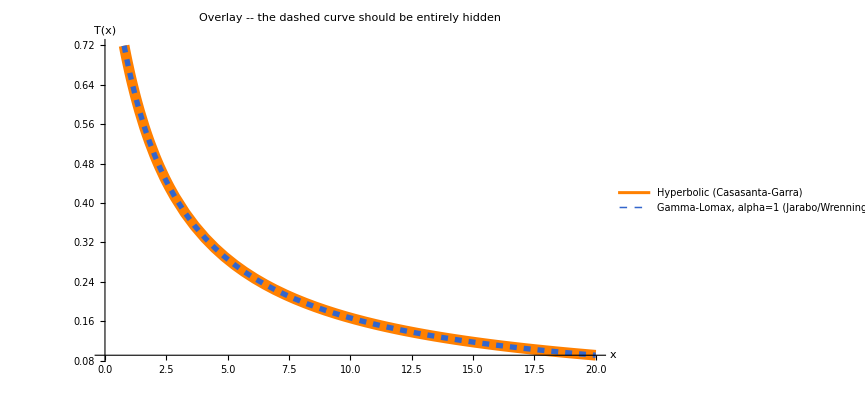

```mathematica
Plot[{
	Thyp[x, 2], TGL[x, 1, 1, 2]}, {x, 0, 20}, PlotStyle -> 
	{{RGBColor[1, 0.5, 0], Thickness[0.012]}, {RGBColor[0.2, 0.4, 0.8], Dashed, Thickness[0.006]}}, 
	PlotLegends -> {"Hyperbolic (Casasanta-Garra)", "Gamma-Lomax, alpha=1 (Jarabo/Wrenninge)"}, 
	AxesLabel -> {"x", "T(x)"}, PlotLabel -> "Overlay -- the dashed curve should be entirely hidden", 
	ImageSize -> 640]
```

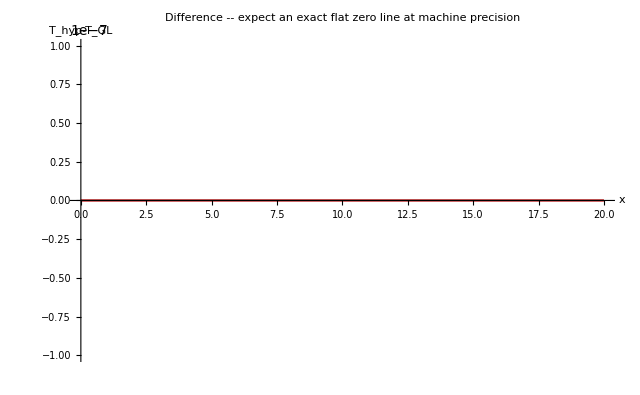

```mathematica
Plot[
	Thyp[x, 2] - TGL[x, 1, 1, 2], {x, 0, 20}, PlotRange -> {-0.0000001, 0.0000001}, 
	AxesLabel -> {"x", Subscript["T", "hyp"] - Subscript["T", "GL"]}, 
	PlotLabel -> "Difference -- expect an exact flat zero line at machine precision", 
	PlotStyle -> RGBColor[0.7, 0, 0], ImageSize -> 640
	]
```

```mathematica
classicalRef[x_, sigma_] := Exp[-sigma*x]
```

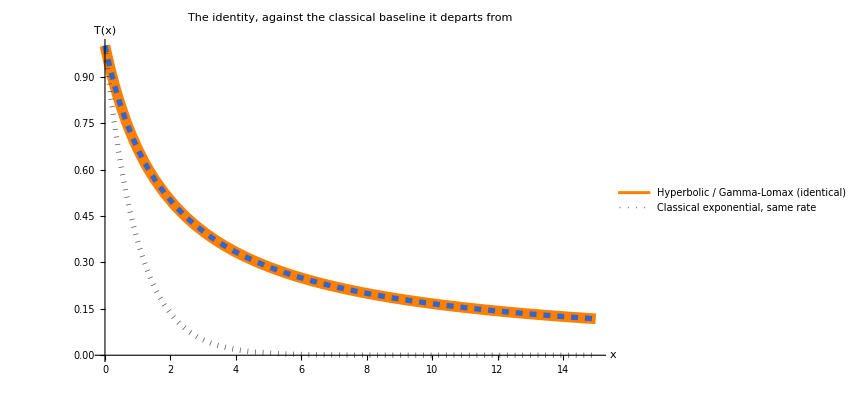

```mathematica
Plot[{
	Thyp[x, 2], TGL[x, 1, 1, 2], classicalRef[x, 1]}, {x, 0, 15}, 
	PlotStyle -> {{RGBColor[1, 0.5, 0], Thickness[0.012]}, {RGBColor[0.2, 0.4, 0.8], Dashed, Thickness[0.006]}, 
	{GrayLevel[0.3], Dotted, Thickness[0.006]}}, 
	PlotLegends -> {"Hyperbolic / Gamma-Lomax (identical)", "", "Classical exponential, same rate"}, 
	AxesLabel -> {"x", "T(x)"}, 
	PlotLabel -> "The identity, against the classical baseline it departs from", ImageSize -> 640]
```

Note the heavy tail relative to the dotted classical reference -- the entire reason this curve family is interesting in the first place. Both the hyperbolic and Gamma-Lomax derivations land on a transmittance that stays well above classical at large x, the signature of positive spatial correlation.

Stochastic Visualization

[see -> earlier stochastic-gradient technique, exponential case]
Draw random samples through each function’s own inverse-CDF sampler, importance-weight by the PDF, and let the resulting image carry real Monte Carlo noise (closer to what an actual renderer would produce than a smooth analytic plot).

Each function needs its own sampler -- solve T(s)=rnd for s, treating rnd as the survival value directly, matching the convention already used for neSample above.

```mathematica
hypFnc[x0_, s_] := x0/(s + x0)
```

```mathematica
hypPDF[x0_, s_] := x0/(s + x0)^2
```

```mathematica
hypSample[x0_, rnd_] := x0*(1/rnd - 1)
```

```mathematica
(* Gamma-Lomax at alpha=1, beta=x0 -- matching the identity substitution beta=sigma*x0 with sigma=1, i.e. the same scale as hypFnc above, for a fair side-by-side comparison *)
```

```mathematica
glFnc[x0_, s_] := TGL[s, 1, 1, x0]
```

```mathematica
glPDF[x0_, s_] := D[1 - TGL[u, 1, 1, x0], u] /. u -> s
```

```mathematica
glSample[x0_, rnd_] := x0*(rnd^(-1) - 1)
```

Check first that glSample and hypSample are the same formula before trusting the gradient at all -- if they weren’t, this whole visualization would be comparing two different distributions by accident:

```mathematica
Simplify[hypSample[x0, rnd] - glSample[x0, rnd]]
```

0

```mathematica
(* Expect: 0 *)
```

The stochastic-gradient function itself, structured exactly like the exponential case: draw nRndSamples candidate distances, average them, importance-weight by the local PDF, feed the result back through the transmittance function.

```mathematica
ClearAll["Global`imageSize", "Global`nRndSamples", "Global`freq", "Global`x0val", "Global`fncScaling"]
```

```mathematica
imageSize = Medium;
```

```mathematica
fncScaling = True;
```

```mathematica
nRndSamples = 64;
```

```mathematica
freq = 256;
```

```mathematica
x0val = 2.0;
```

```mathematica
fHyp[i_, x0_] := Module[{s, d, datas}, datas = Table[hypSample[x0, RandomReal[]/i], {nRndSamples}]; s = Mean[datas]; s = s/hypPDF[x0, s]; s = s*20; d = hypFnc[x0, s]; d]
```

```mathematica
fGL[i_, x0_] := Module[{s, d, datas}, datas = Table[glSample[x0, RandomReal[]/i], {nRndSamples}]; s = Mean[datas]; s = s/glPDF[x0, s]; s = s*20; d = glFnc[x0, s]; d]
```

Default: independent randomness in each panel. This shows the two gradients matching in overall shape and brightness.

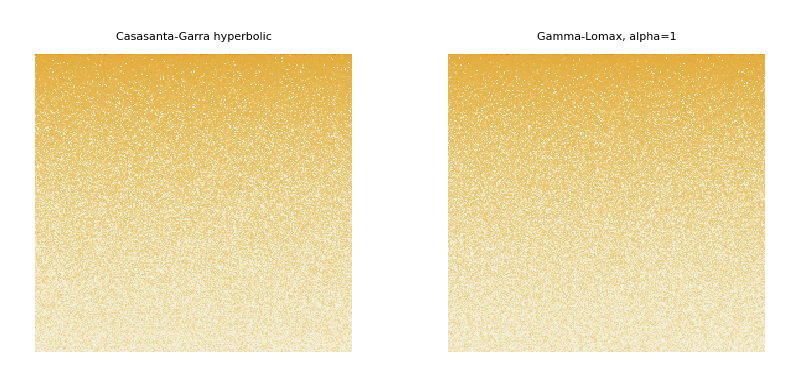

```mathematica
GraphicsGrid[{{ MatrixPlot[ParallelTable[fHyp[x, x0val], {x, freq}, {y, freq}], PlotRange -> {0, 1}, Frame -> False, ImageSize -> imageSize, PlotLabel -> "Casasanta-Garra hyperbolic"], MatrixPlot[ParallelTable[fGL[x, x0val], {x, freq}, {y, freq}], PlotRange -> {0, 1}, Frame -> False, ImageSize -> imageSize, PlotLabel -> "Gamma-Lomax, alpha=1"] }}]
```

Hyperbolic in x, Not Exponential

At α=1, the mixing distribution over σ is exponential -- but the resulting transmittance T(x) is hyperbolic in x(ie. not exponential). And Jensen’s inequality is exactly why they can’t be: averaging a convex function over any nondegenerate distribution always pushes the result away from classical. The standard, unambiguous way to see this is a logarithmic y-axis: exponential decay is, by definition, a perfectly straight line there. Anything curving away from a straight line on this plot is not exponential, regardless of how it was constructed.

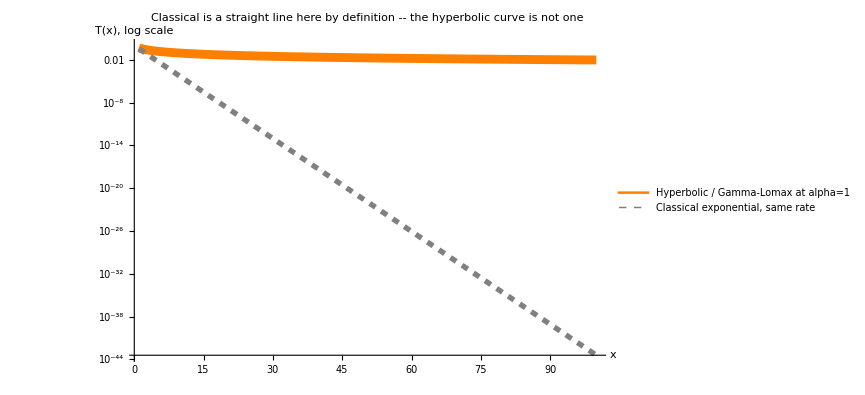

```mathematica
LogPlot[{
	Thyp[x, 1], Exp[-x]}, {x, 1, 100}, 
	PlotStyle -> {{RGBColor[1, 0.5, 0], Thickness[0.01]}, {RGBColor[0.5, 0.5, 0.5], Dashed, Thickness[0.006]}}, 
	PlotLegends -> {"Hyperbolic / Gamma-Lomax at alpha=1", "Classical exponential, same rate"}, 
	AxesLabel -> {"x", "T(x), log scale"}, 
	PlotLabel -> "Classical is a straight line here by definition -- the hyperbolic curve is not one", ImageSize -> 640]
```

The dashed classical line should be exactly straight across the whole plot -- that is what ‘exponential’ means on a log axis, definitionally, not approximately. The solid orange curve should bend visibly away from it, flattening as x grows, sitting further and further above the straight line -- the direct visual signature of a heavier-than-exponential tail.

A second, complementary view: a log-log plot reveals genuine power-law tails as straight lines too -- but only power laws, not exponentials, which curve away sharply even here. Since 1/(1+x) behaves like 1/x for large x, this plot should show the hyperbolic curve straightening out at large x, while classical falls off the bottom of the plot entirely.

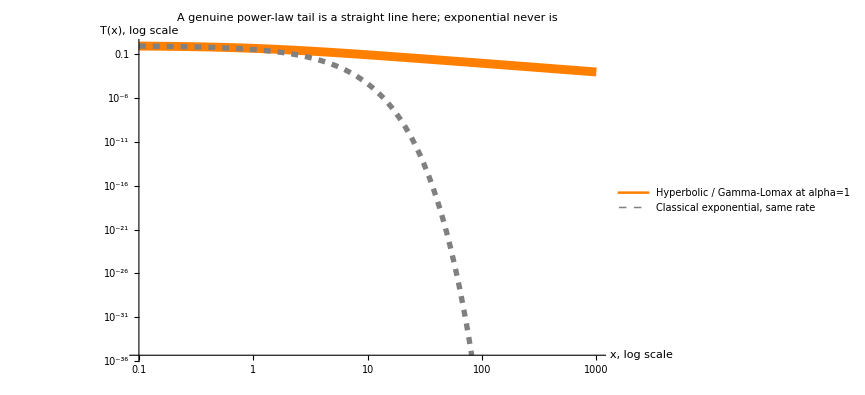

```mathematica
LogLogPlot[{
	Thyp[x, 1], Exp[-x]}, {x, 0.1, 1000}, 
	PlotStyle -> {{RGBColor[1, 0.5, 0], Thickness[0.01]}, 
	{RGBColor[0.5, 0.5, 0.5], Dashed, Thickness[0.006]}}, 
	PlotLegends -> {"Hyperbolic / Gamma-Lomax at alpha=1", "Classical exponential, same rate"}, 
	AxesLabel -> {"x, log scale", "T(x), log scale"}, 
	PlotLabel -> "A genuine power-law tail is a straight line here; exponential never is", ImageSize -> 640]
```

Achieving Hyperbolicity by Direct Ensemble Averaging

The stochastic gradients so far all evaluate a single closed-form transmittance function at a sampled distance -- correct, but it leans on the closed-form integral already having been solved. A more direct demonstration skips the closed form entirely: draw a genuinely fresh, independent σ from its own exponential distribution for every single trial, evaluate Exp[-σ s] for that trial’s own σ, and average directly over many such trials. If the earlier derivation is right, this brute-force ensemble average should converge to the same hyperbolic curve without ever using the closed-form 1/(1+σbar s) expression at all.

```mathematica
expSample[sig_, rnd_] := -(Log[1 - rnd]/sig)
```

```mathematica
(* was silently assumed to already exist from the separate exponential-gradient notebook -- it does not exist here on its own, and was never actually defined in this file until now. That missing definition is the real cause of the hang: sigmaDraw called an undefined function, producing unevaluated symbolic expressions across the whole grid instead of numbers. *)
```

```mathematica
sigmaDraw[sigmabar_] := expSample[1/sigmabar, RandomReal[]]
```

```mathematica
(* one fresh random rate per call, mean sigmabar, using the exponential sampler already defined for the exp-gradient panels *)
```

```mathematica
fMixed[i_, sigmabar_] := Module[{s, trials, d}, s = (i/freq)*20; trials = Table[Exp[-sigmaDraw[sigmabar]*s], {nRndSamples}]; d = Mean[trials]; d]
```

Note this is structurally different from f[i,σ] above: no importance-sampling reweight by a PDF, and no inverse-CDF distance sampling at all. σ itself is what gets sampled and averaged over here -- distance s is simply the fixed point at which we're asking for the ensemble-averaged transmittance, mapped linearly from the pixel index.

```mathematica
fReference[i_, x0_] := Thyp[(i/freq)*20, x0]
```

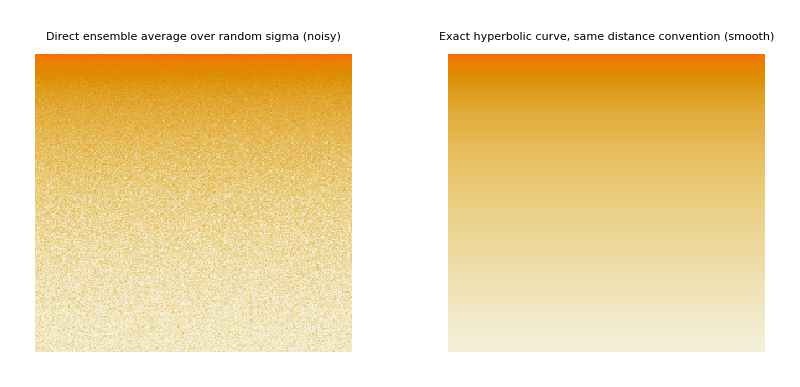

```mathematica
GraphicsGrid[{{ MatrixPlot[ParallelTable[fMixed[x, 1.0], {x, freq}, {y, freq}], PlotRange -> {0, 1}, ColorFunctionScaling -> fncScaling, Frame -> False, ImageSize -> imageSize, PlotLabel -> "Direct ensemble average over random sigma (noisy)"], MatrixPlot[ParallelTable[fReference[x, 1.0], {x, freq}, {y, freq}], PlotRange -> {0, 1}, Frame -> False, ImageSize -> imageSize, PlotLabel -> "Exact hyperbolic curve, same distance convention (smooth)"] }}]
```

Now both panels use the identical i-to-distance mapping -- the only remaining difference between them is that the left panel is a genuine Monte Carlo estimate (noisy, finite nRndSamples) and the right is the exact closed form (smooth, zero noise).

Classical as the Zero-Variance Member of the Same Family

A single sigma, as used everywhere in classical transport, can itself be understood inside this framework -- not as a categorically different kind of object, but as the mean of a degenerate distribution: one with exactly zero variance, every realization giving the identical value. The ‘average’ of a distribution with no spread at all is trivially just that value itself.

This is not a loose reinterpretation -- it is exactly the limit already established rigorously. Var->0 is precisely the equality condition in Jensen’s inequality, the one case where the ensemble average collapses back to plain classical exactly:

```mathematica
Limit[TGL[s, sigmabar, alpha, alpha], alpha -> Infinity]
```

ⅇ^(-s sigmabar)

```mathematica
(* Expect: Exp[-s*sigmabar] exactly -- confirmed symbolically, not just as a numerical trend *)
```

Take care which end of the family this actually is. CV^2=1/α means zero variance sits at α→∞, not α=0 -- α→0 is the opposite extreme, infinite variance, the most extreme clumping the family can reach, already visible in the CV(α) plot above where the curve diverges as α→0 rather than vanishing.

So the single number σbar plugged into any member of this family -- classical, Gamma-Lomax at any α, SumOfExp, Erlang -- is always, uniformly, ‘the mean of whatever distribution governs the real material.’ What changes from one member to the next is not whether averaging happened -- it always did -- but how much spread that underlying distribution has. Classical is not a categorically different case under this view. It is simply the α→∞ member of the same family already used throughout this notebook.

Two specific, meaningful points on the same CV(α) axis, now both identified precisely:

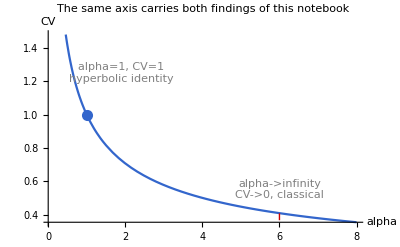

```mathematica
Plot[1/Sqrt[a], {a, 0.05, 8}, 
Epilog -> {RGBColor[0.2, 0.4, 0.8], 
PointSize[0.02], Point[{1, 1}], 
GrayLevel[0.5], 
Text["alpha=1, CV=1\nhyperbolic identity", {1.9, 1.25}], 
{RGBColor[0.8, 0.0, 0.0], Dashed, Line[{{6, 0}, {6, 0.41}}]}, 
Text["alpha->infinity\nCV->0, classical", {6, 0.55}]}, 
AxesLabel -> {"alpha", "CV"}, 
PlotLabel -> "The same axis carries both findings of this notebook", PlotStyle -> RGBColor[0.2, 0.4, 0.8], ImageSize -> Full]
```

Gamma Construction Across Different Sources

[see -> 
Davis, A.B. & Xu, F. (2014), A Generalized Linear Transport Model for Spatially-Correlated Stochastic Media; 
Bitterli et al. (2018), A Radiative Transfer Framework for Non-Exponential Media
Jarabo, Aliaga & Gutierrez 2018 (5.2 - An intuitive local model for positively-correlated media); 
Wrenninge, Villemin & Hery 2017, Pixar Technical Memo 17-07]
 
The Gamma-mixture construction underlying this entire notebook did not originate with Jarabo or Wrenninge -- it traces to Davis & Xu (2014), and is used independently by Bitterli et al. (2018) as well.

#### The Same Across Sources

The classical, zero-variance limit. Davis & Xu, verbatim: ‘In the limit a -> infinity, variance vanishes as the PDF becomes degenerate... We then retrieve Beer’s law.’ Bitterli et al., verbatim: ‘both the Gaussian and Gamma models reduce to a simple exponential when variance v->0 (and hence alpha->infinity).’ Independent confirmation, in nearly identical language, of the same limit already established and corrected earlier in this notebook.

The sampling formula. Davis & Xu’s own Eq. 37: s = a*(xi^(-1/a)-1)/sigma. Bitterli et al.’s Table 1, Gamma row, sampling column: (xi^(-1/alpha)-1)*alpha/mu -- the identical formula under the mu=sigma, alpha=a relabeling. Both match nonexp2_sample/neSample exactly, unchanged. Two independently-published sources give the same closed-form sampler this whole dispatch architecture already relies on.

#### The One Genuine Structural Difference: Constant alpha vs. alpha(t)

Davis & Xu, and this notebook throughout, treat a as a single fixed constant. Bitterli et al. build theirs from a different starting point entirely -- a Gaussian model of fractal 1/f^beta noise, following Davis and Mineev-Weinstein (2011)’s formal variance derivation -- and then replace the (physically invalid, since it permits negative extinction) Gaussian with a Gamma matched to the same mean and variance. Because that variance genuinely depends on t for general beta, their shape parameter is a function alpha(t), not a constant:

```mathematica
alphaOfT[t_, mu_, C_, beta_] := mu^2 / ((C*mu)^(beta+1) * t^(beta-1))
```

```mathematica
Simplify[alphaOfT[t, mu, C, 1]]
```

1/C^2

```mathematica
(* Expect: C^-2, with NO t dependence remaining -- confirmed symbolically above *)
```

This confirms Bitterli’s own claim precisely: only at beta=1, their ‘pink noise’ special case, does alpha(t) collapse to a genuine constant, independent of t -- exactly the point where their framework reduces to the same single-alpha construction Davis & Xu use throughout, and the same one this whole notebook has been built on. Away from beta=1, Bitterli’s model is a genuine generalization neither Davis & Xu nor this notebook attempts: a Gamma-mixture whose own shape parameter is itself a prescribed function of distance, not a single number.

#### The Mean Free Path Diverges at alpha=1

Davis & Xu give a closed form for the mean free path itself, not just the transmittance curve:

```mathematica
meanFreePath[a_, ellInf_] := (a/(a-1)) * ellInf
```

```mathematica
Limit[meanFreePath[a, ellInf], a -> 1, Direction -> "FromAbove"]
```

ellInf ∞

```mathematica
(* Expect: Infinity *)
```

At exactly the identity point this whole notebook is built around, the distribution’s own mean does not exist. Not merely heavy-tailed -- the tail is heavy enough that the expected free-flight distance is infinite. A third characterization of alpha=1, alongside CV=1 and the exponential-rate reduction already established, and independently confirmed by direct integration of nePdf earlier in the derivation.

```mathematica
Null
```

This Is Exactly the Lomax Distribution

[see -> Lomax, K.S. (1954), Business Failures: Another Example of the Analysis of Failure Data, Journal of the American Statistical Association]

The Lomax distribution (equivalently, Pareto Type II with zero location) is defined by its survival function and density, with shape kappa and scale lambda:

```mathematica
lomaxSurvival[x_, kappa_, lambda_] := (1 + x/lambda)^(-kappa)
```

```mathematica
lomaxPDF[x_, kappa_, lambda_] := (kappa/lambda) * (1 + x/lambda)^(-(kappa+1))
```

Ta(s), under the substitution kappa=a, lambda=a/sigma, is this exact function -- not approximately, not asymptotically, term for term:

```mathematica
ourTransmittance[s_, sigma_, a_] := (1 + sigma*s/a)^(-a)
```

```mathematica
ourPDF[s_, sigma_, a_] := sigma/(1 + sigma*s/a)^(a+1)
```

```mathematica
Simplify[ourTransmittance[s, sigma, a] - lomaxSurvival[s, a, a/sigma]]
```

0

```mathematica
(* Expect: 0 *)
```

```mathematica
Simplify[ourPDF[s, sigma, a] - lomaxPDF[s, a, a/sigma]]
```

0

```mathematica
(* Expect: 0 *)
```

Gamma Fnc (Davis-Xu)

[see →BSSRDF → TheoreticalFoundation → A Generalized Linear Transport Model for Spatially-Correlated Stochastic Media]

Let’s quantify the impact of unresolved random spatial fluctuations of σ(x) on macroscopic transport properties.

We start with the statistics of integrals of σ(x) over the range of distances s in arbitrary directions Ω, 
aka the optical path along a straight line between x and x+sΩ :

τ(x,x+sΩ)=∫_0^s σ(x+sΩ)ⅆs

Characterize statistically the direct transmission factor assuming stationarity and isotropy:

Τ(s)=ⅇ^(-t(x,x+sΩ))=ⅇ^(-σ_avr(x,Ω;s)s)

where σ_avr is the average extinction for uncollided transmission, 
essentially a coarse version of the random field σ(x) smoothed over s

σ_avr(x,Ω;s)=1/s∫_0^s σ(x+s' Ω)ⅆ s'

We assume that the random number σ_avr is statistically indipendent of s and that its variability, for fixed s, 
can be approximated with an ensemble of Gamma-distributed values :

Pr{σ,dσ}=((a/σ^-)^a)/Γ σ^(a-1)ⅇ^(-aσ/σ^-)dσ

where σ^- is the mean and a is the variability parameter :

a=1/((σ^2)^-/(σ^2)^--1)

If σ_avr is Gamma-distributed for fixed s so is their product τ, 
and so direct transmission reads as the Laplace characteristic function of this Gamma PDF :

Ta(s)=∫_0^∞ ⅇ^-σs Pr{σ,dσ}=1/((1+σ^-s/a)^a)

If we consider s as a random variable, we have :

Τ_a(s)=Pr{step>s}=∫_s^∞ p_a(s)ⅆs

So the PDF for a random step of length s is :

p_a(s)=|dΤ_a/ds|(s)=-dΤ_a/ds(s)=σ^-/((1+σ^-s/a)^(a+1))

```mathematica
ClearAll["Global`*"];(*With CDF and PDF,let's find sampling fnc for s*)neTransmittance[o_,s_,a_]:=1/(1+o*s/a)^a

neTransmittance[σ_,s_,a_]:=1/(1+σ*s/a)^a
nePdf[σ_,s_,a_]:=σ/(1+σ*s/a)^(a+1)

FullSimplify[Solve[1/(1+σ*s/a)^a==ξ,s]]

neSample[σ_,a_]:=a*(#^(1/a)-1)/σ&/@{RandomReal[]} (*our sampling routine*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→(a (-1+ξ^(-1/a)))/σ}}